## Code

```mathematica
Remove["Global`*"];
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
(*Gibbs sampling from 3 conditional distributions*)
(*P     - prices vector
qinit - initial values for q, a vector of size Length[P]
σinit - initial value for σ
μc    - prior parameter for truncated normal distribution mean
Ωc    - prior parameter for truncated normal distribution standard deviation
AlphaPrior - alpha parameter for gamma distribution prior for σ
BetaPrior - beta parameter for gamma distribution prior for σ*)
```

```mathematica
Gibbss[P_,qinit_,σinit_,μc_,Ωc_,AlphaPrior_,BetaPrior_,sweep1_,OptionsPattern[]]:=Module[{σ=σinit,
q=qinit,qdummy,c=0,ΔP=Δ[P],n=Length[P]},
Table[
(*update q vector after first and every next sweep fro values from array q[i]*)
(*Begin with starting values of q*)
Table[qdummy[i]:=q[[i]],{i,n}];
c=GenerateC[ΔP,Δ[q],σ,μc,Ωc];
σ=Generateσ[ΔP,c,Δ[q],AlphaPrior,BetaPrior,n-1];
q=Generateq[ΔP,c,σ,n,qdummy];
{σ,c,q},
{sweep1}]
]
```

```mathematica
(*_______________________________________________________generating c_____________________________________________________*)
```

```mathematica
Options[GenerateC]={DistributionParameter1->{0,∞}};
GenerateC[ΔP_,Δq_,σ_,μc_,Ωc_,OptionsPattern[]]:=RandomVariate[
dist[
OptionValue[DistributionParameter1],
μpost[ΔP,Δq,σ,μc,Ωc],
Sqrt@PosteriorCov[Δq,σ,Ωc]
]
];
```

```mathematica
(*Creating function for truncated normal distribution*)
```

```mathematica
dist[truncRegion_,distPar1_,distPar2_]:=TruncatedDistribution[truncRegion,NormalDistribution[distPar1,distPar2]]
```

```mathematica
(*Functions for Creating posteriors for μc and Ωc
```

```mathematica
μpost[ΔP_,Δq_,σ_,μc_,Ωc_]:=d[ΔP,Δq,σ,μc,Ωc]*𝔻[Δq,σ,Ωc](*P0sterior mean of c as a function of d and SigmaPost (posterior standard error of estimate)*)
𝔻i[Δq_,σ_,Ωc_]:=Total[Δq*Δq]/σ^2+1/Ωc^2
𝔻[Δq_,σ_,Ωc_]:=1/𝔻i[Δq,σ,Ωc];
PosteriorCov[Δq_,σ_,Ωc_]:=𝔻[Δq,σ,Ωc];
(*posterior standard error of estimate*)
d[ΔP_,Δq_,σ_,μc_,Ωc_]:=1/σ^2 Total[ΔP*Δq]+μc/Ωc^2(*Look any text on bayes regression, only difference is that we are using here univariate regression*)
```

```mathematica
(*___________________________________________________generating σ____________________________________________________________*)
```

```mathematica
Generateσ[ΔP_,c_,Δq_,AlphaPrior_,BetaPrior_,N_]:=1/Sqrt[Generateσsqrℐnverse[ΔP,c,Δq,AlphaPrior,BetaPrior,N]];
```

```mathematica
e[ΔP_,c_,Δq_]:=ΔP-c  Δq(*residuals from bayes regression*)
AlphaPost[AlphaPrior_,N_]:=AlphaPrior+N/2(*alpha posterior*)
BetaPost[BetaPrior_,ΔP_,c_,Δq_]:=BetaPrior+Total[(e[ΔP,c,Δq]^2)]/2(*beta posterior*)
(*generate σsqr posterior from gamma dist*)
Generateσsqrℐnverse[ΔP_,c_,Δq_,AlphaPrior_,BetaPrior_,N_]:=RandomVariate[
GammaDistribution[AlphaPost[AlphaPrior,N],1/BetaPost[BetaPrior,ΔP,c,Δq]
]
]
```

```mathematica
(*____________________________Generating latent time series of q's, depending on case, 1st, middle or last______________________*)
```

```mathematica
Generateq[ΔP_,c_,σ_,n_,qdummy_]:=Table[
If[i==1,qdummy[i]=Generate𝒬First[qdummy[i+1],ΔP[[i]],c,σ],
If[i==n,qdummy[i]=Generate𝒬Last[qdummy[i-1],ΔP[[i-1]],c,σ],
qdummy[i]=Generate𝒬T[qdummy[i-1],qdummy[i+1],ΔP[[i-1]],ΔP[[i]],c,σ]]],{i,n}
];
```

```mathematica
Generate𝒬T[qbefore_,qafter_,ΔP1_,ΔP2_,c_,σ_]:=RandomChoice[{q𝒟istT[qbefore,qafter,ΔP1,ΔP2,c,σ][1],q𝒟istT[qbefore,qafter,ΔP1,ΔP2,c,σ][-1]}->{1,-1}];
q𝒟istT[qbefore_,qafter_,ΔP1_,ΔP2_,c_Real,σ_][q_]:=Evaluate[ⅇ^((c^2 (4-2 q^2+qafter^2+qbefore^2+2 q (qafter+qbefore))+2 c (q+qbefore) ΔP1+ΔP1^2-2 c (q+qafter) ΔP2+ΔP2^2)/(2 σ^2))/(ⅇ^(((c+c qbefore+ΔP1)^2+(c+c qafter-ΔP2)^2)/(2 σ^2))+ⅇ^(((c (-1+qbefore)+ΔP1)^2+(c-c qafter+ΔP2)^2)/(2 σ^2)))];
Generate𝒬First[q2_,ΔP1_,c_,σ_]:=RandomChoice[{q𝒟istFirst[q2,ΔP1,c,σ][1],q𝒟istFirst[q2,ΔP1,c,σ][-1]}->{1,-1}];
q𝒟istFirst[q2_,ΔP1_,c_,σ_][q_]:=Evaluate[(ⅇ^((c^2 (2-q^2+2 q q2+q2^2)-2 c (q+q2) ΔP1+ΔP1^2)/(2 σ^2)))/(ⅇ^((c+c q2-ΔP1)^2/(2 σ^2))+ⅇ^((c-c q2+ΔP1)^2/(2 σ^2)))];
Generate𝒬Last[qbefore_,ΔP_,c_,σ_]:=RandomChoice[{q𝒟istLast[qbefore,ΔP,c,σ][1],q𝒟istLast[qbefore,ΔP,c,σ][-1]}->{1,-1}];
q𝒟istLast[qbefore_,ΔPbefore_,c_,σ_][q_]:=Evaluate[(ⅇ^((c^2 (2-q^2+2 q qbefore+qbefore^2)+2 c (q+qbefore) ΔPbefore+ΔPbefore^2)/(2 σ^2)))/(ⅇ^((c (-1+qbefore)+ΔPbefore)^2/(2 σ^2))+ⅇ^((c+c qbefore+ΔPbefore)^2/(2 σ^2)))];
```

```mathematica
(*_______________________________________Differencing time series function______________________________________________________*)
```

```mathematica
Δ[x_List]:=x[[2;;All]]-x[[1;;-2]];
```

## Example

### Simulating prices with given parameters:

```mathematica
SeedRandom[10]
Nu=20;
σ=0.01;
ur=RandomVariate[NormalDistribution[0,σ],Nu];
qr=RandomChoice[{-1,1},Nu];
t=0;cr=0.010;
mr=Table[t=t+ur[[i]],{i,Length[ur]}];
P=mr+qr cr;
f=Sign/@Δ[P];
f=Prepend[f,1];
ΔP=Δ[P];
```

### Defining initial values, number of sweeps and running sampler:

```mathematica
sweep=5000;
burn=sweep/5;
σinit=0.01;
μc=0;
Ωc=1;
αprior=10^-6;
βprior=10^-6;
a=Gibbss[P,f,σinit,μc,Ωc,αprior,βprior,sweep];//AbsoluteTiming
```

{11.5844,Null}

### Ploting posterior distributions and series of q:

#### Posterior distribution graph of c

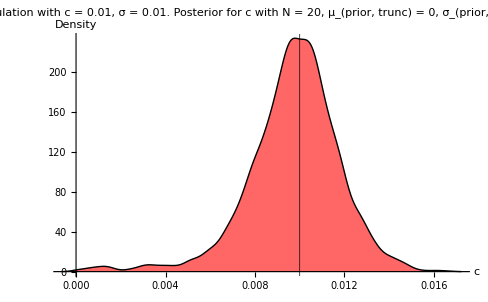

```mathematica
GraphC=SmoothHistogram[
a[[All,2]][[burn;;All]],
PlotRange->All,
Filling->Axis,FillingStyle->Directive[Opacity[.6],Red],
PlotLabel->Style["Simulation with c = "<>ToString[cr]<>", σ = "<>ToString[σ]<>". Posterior for c with N = "<>ToString@Nu<>", μ_(prior, trunc) = 0, σ_(prior, trunc) = 1",Black,FontFamily->"Times New Roman"],
AxesLabel->{"c","Density"},AxesStyle->Directive[FontFamily->"Times New Roman",Black],
PlotStyle->Directive[Thick,Black],
GridLines->{{{cr,Directive[Thick,Black,Opacity[1]]}}}
]
```

#### Posterior distribution graph of σ

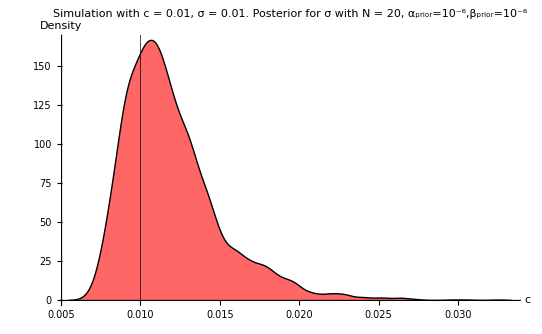

```mathematica
Graphσ=SmoothHistogram[
a[[All,1]][[burn;;All]],
PlotRange->All,
Filling->Axis,FillingStyle->Directive[Opacity[.6],Red],
PlotLabel->Style["Simulation with c = "<>ToString[cr]<>", σ = "<>ToString[σ]<>". Posterior for σ with N = "<>ToString@Nu<>", α_prior=10^-6,β_prior=10^-6",Bold,Black,FontFamily->"Times New Roman"],
AxesLabel->{"c","Density"},AxesStyle->Directive[FontFamily->"Times New Roman",Black],
PlotStyle->Directive[Thick,Black],
GridLines->{{{σ,Directive[Thick,Black,Opacity[1]]}}}
]
```

#### Posterior distribution graph of q

```mathematica
gibbsq=a[[burn;;All,3]];
gibbsqmean=Table[Mean[gibbsq[[All,i]]],{i,Nu}];
gibbsround=Table[If[Mean[gibbsq[[All,i]]]>0,1,-1],{i,Nu}];
NuOfHits=Table[If[gibbsround[[i]]==qr[[i]],1,0],{i,Nu}]//Total;
```

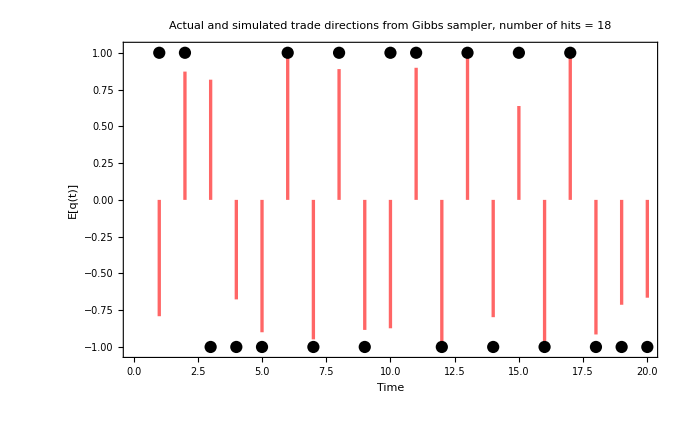

```mathematica
Graphq=ListPlot[
{f,gibbsqmean},
PlotRange->{-1.03,1.03},
Frame->True,FrameStyle->Directive[Black,FontFamily->"Times New Roman",Black],FrameLabel->{Style["Time",FontFamily->"TimesNewRoman",13],Style["E[q(t)]",FontFamily->"TimesNewRoman",13]},
Filling->{1->None,2->Axis},FillingStyle->Directive[Thickness[0.0035],Red,Opacity[0.6]],
AxesStyle->Directive[FontFamily->"Times New Roman",Black],
PlotLabel->Style["Actual and simulated trade directions from Gibbs sampler, number of hits = "<>ToString@NuOfHits,Bold,Black,FontFamily->"Times New Roman",13],
PlotStyle->{Directive[Black],Directive[Opacity[0]]},
Epilog->{Text[Style["+1 (Buy)",Black,FontFamily->"Times New Roman",13],{-1,1.1}],
Text[Style["-1 (Sell)",Black,FontFamily->"Times New Roman",13],{-1,-1.1}]},
ImagePadding->40,PlotRangeClipping->False
]
```

#### Joint density c and q plot

```mathematica
data=a[[All,{1,2}]][[burn;;All]];
```

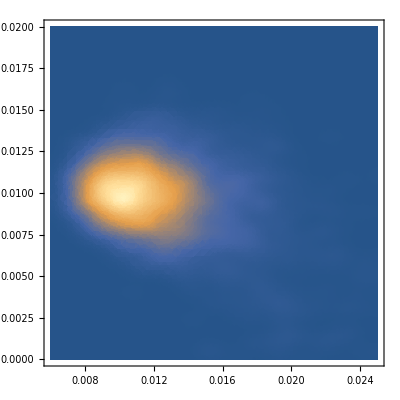

```mathematica
SmoothDensityHistogram[data,Mesh->20,PlotRange->{{0.006,0.025},{0,0.02}}]
```

```mathematica
SmoothHistogram3D[data,PlotRange->All]
```

-Graphics3D-